# Impact of Parameter Perturbation on the Neural Network Performance

This project investigates the impact of perturbing parameters of a trained neural network on its performance by adding random noise drawn from different distributions to weights and biases of different layers.

## Introduction

to observe the effects of perturbing the weights and biases of the neural network. It

## The LeNet Model1

#### Introduction

LeNet Model is a convolutional neural network for image classification developed by Yann LeCun and his collaborators at AT&T Bell Labs. It is known to have achieved a significantly high performance with an error rate less than 1% per each handwritten digit. LeCun’s work is known to be the first attempt to successfully train CNNs using gradient-based optimization.

```mathematica
leNet = NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<11>]

#### Architecture

LeNet comprises two main parts: two convolutional layers  with max pooling and two fully connected layers. The summary graphic of the LeNet is shown below.

```mathematica
Information[leNet,"FullSummaryGraphic"]
```

-Graphics-

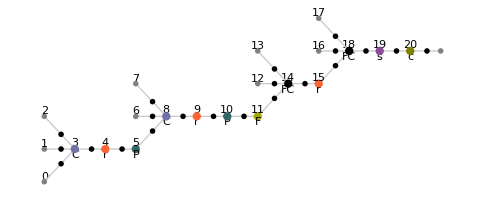

```mathematica
Information[ NetModel["LeNet Trained on MNIST Data"],"MXNetNodeGraphPlot"]
```

## The MNIST Dataset2

The LeNet is was trained on the MNIST dataset of handwritten digits and is known to have achieved 98.5% accuracy on the MNIST test dataset.

### Importing MNIST Test Dataset

The MNIST database consists of a training set of 60,000 examples and a test set of 10,000 examples.

```mathematica
mnistTest=ResourceData["MNIST","TestData"];
```

## Exploratory Data Analysis (EDA)

## Extracting the Weights and Biases of the LeNet

We extract the weights and biases from the LeNet for each layer. The 1st (Convolutional), 4th (Convolutional), 8th (Linear) and 10th (Linear) layers have weights.

```mathematica
layerWeights = Table[NetExtract[leNet,{n,"Weights"}],{n,{1,4,8,10}}]
```

{NumericArray[…],NumericArray[…],NumericArray[<500,800>, Real32],NumericArray[…]}

```mathematica
layerBiases = Table[NetExtract[leNet,{n,"Biases"}],{n,{1,4,8,10}}]
```

{NumericArray[…],NumericArray[…],NumericArray[…],NumericArray[…]}

## Summary Statistics - Weights Distribution

#### Graphical Summary

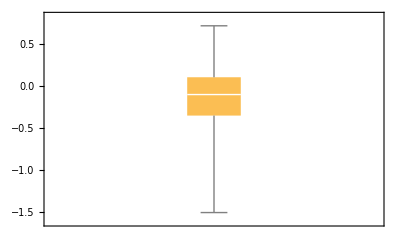
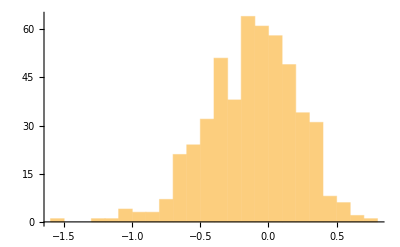
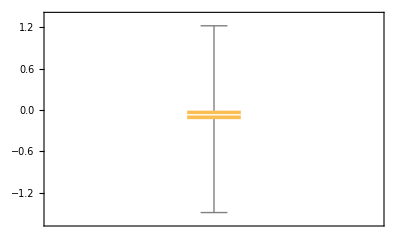
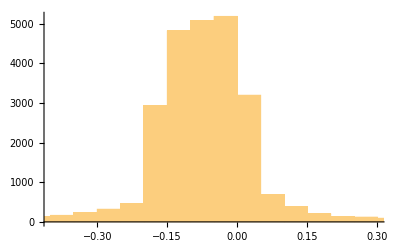
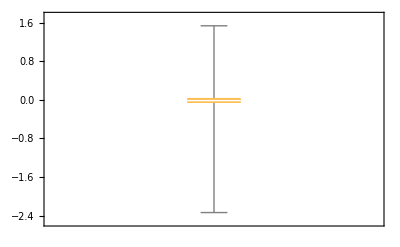
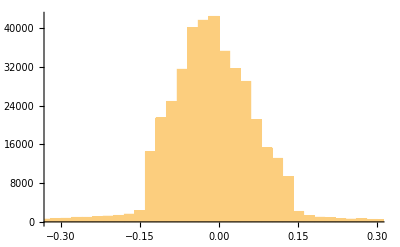
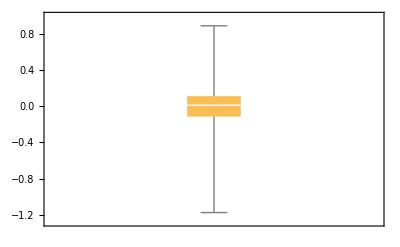
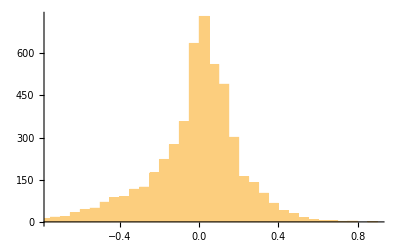
Weights Distribution
Layer 1
(Convolutional) | -Graphics- | -Graphics-
Layer 4
(Convolutional) | -Graphics- | -Graphics-
Layer 8
(Linear) | -Graphics- | -Graphics-
Layer 10
(Linear) | -Graphics- | -Graphics-

```mathematica
Grid[
{
{Style["Weights Distribution",FontSize->20, FontWeight->Bold]},
{TableForm[Table[{BoxWhiskerChart[Flatten[layerWeights[[l]]//Normal]],Histogram[Flatten[layerWeights[[l]]//Normal]]},{l,1,4}],TableHeadings->{{"Layer 1\n(Convolutional)","Layer 4\n(Convolutional)","Layer 8\n(Linear)","Layer 10\n(Linear)"}}]}
},
Spacings->{2,1}
]
```

#### Numerical Summary

```mathematica
Grid[
{{Style["Weights Distribution",FontSize->20, FontWeight->Bold]},
{TableForm[Transpose[Table[
{
Mean[Flatten[layerWeights[[l]]//Normal]],
StandardDeviation[Flatten[layerWeights[[l]]//Normal]],
Min[Flatten[layerWeights[[l]]//Normal]],
Max[Flatten[layerWeights[[l]]//Normal]],
Median[Flatten[layerWeights[[l]]//Normal]],
(Max[Flatten[layerWeights[[l]]//Normal]]-Min[Flatten[layerWeights[[l]]//Normal]]),
InterquartileRange[Flatten[layerWeights[[l]]//Normal]]
},
{l,1,4}
]],
TableHeadings->{{"Mean","Standard Deviation","Min","Max","Median","Range","IQR"},{"Layer 1\n(Convolutional)","Layer 4\n(Convolutional)","Layer 8\n(Linear)","Layer 10\n(Linear)"}}
]}},
Spacings->{2,1}
]
```

Weights Distribution
 | Layer 1
(Convolutional) | Layer 4
(Convolutional) | Layer 8
(Linear) | Layer 10
(Linear)
Mean | -0.1234 | -0.075064 | -0.0162563 | -0.019502
Standard Deviation | 0.332887 | 0.150124 | 0.117813 | 0.226538
Min | -1.5101 | -1.49051 | -2.33753 | -1.17305
Max | 0.720769 | 1.22129 | 1.53562 | 0.885933
Median | -0.10042 | -0.0711243 | -0.0159563 | 0.0103053
Range | 2.23087 | 2.7118 | 3.87316 | 2.05898
IQR | 0.457827 | 0.123344 | 0.104697 | 0.225497

## Summary Statistics - Weights Distribution

#### Graphical Summary

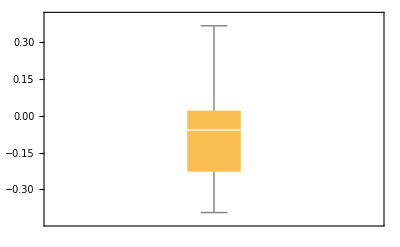
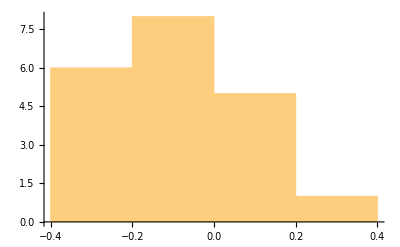
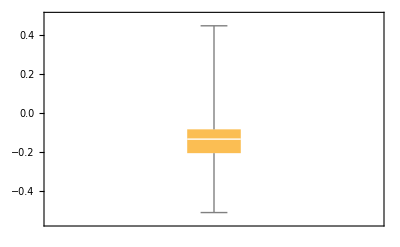
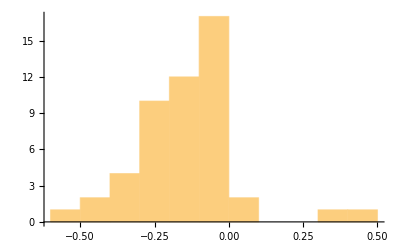
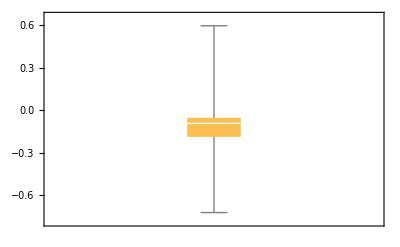
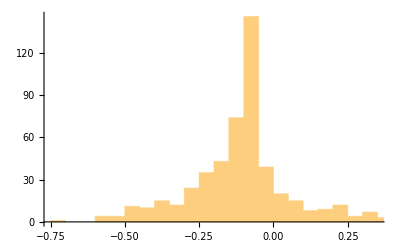
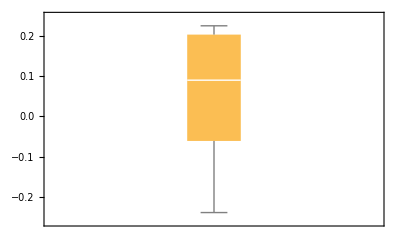
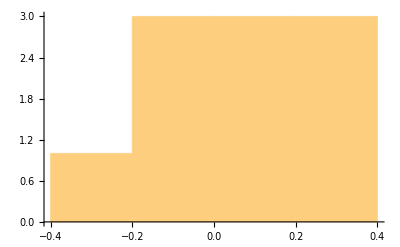
Biases Distribution
Layer 1
(Convolutional) | -Graphics- | -Graphics-
Layer 4
(Convolutional) | -Graphics- | -Graphics-
Layer 8
(Linear) | -Graphics- | -Graphics-
Layer 10
(Linear) | -Graphics- | -Graphics-

```mathematica
Grid[
{
{Style["Biases Distribution",FontSize->20, FontWeight->Bold]},
{TableForm[Table[{BoxWhiskerChart[Flatten[layerBiases[[l]]//Normal]],Histogram[Flatten[layerBiases[[l]]//Normal]]},{l,1,4}],TableHeadings->{{"Layer 1\n(Convolutional)","Layer 4\n(Convolutional)","Layer 8\n(Linear)","Layer 10\n(Linear)"}}]}
},
Spacings->{2,1}
]
```

#### Numerical Summary

```mathematica
Grid[
{{Style["Biases Distribution",FontSize->20, FontWeight->Bold]},
{TableForm[Transpose[Table[
{
Mean[Flatten[layerBiases[[l]]//Normal]],
StandardDeviation[Flatten[layerBiases[[l]]//Normal]],
Min[Flatten[layerBiases[[l]]//Normal]],
Max[Flatten[layerBiases[[l]]//Normal]],
Median[Flatten[layerBiases[[l]]//Normal]],
(Max[Flatten[layerBiases[[l]]//Normal]]-Min[Flatten[layerBiases[[l]]//Normal]]),
InterquartileRange[Flatten[layerBiases[[l]]//Normal]]
},
{l,1,4}
]],
TableHeadings->{{"Mean","Standard Deviation","Min","Max","Median","Range","IQR"},{"Layer 1\n(Convolutional)","Layer 4\n(Convolutional)","Layer 8\n(Linear)","Layer 10\n(Linear)"}}
]}},
Spacings->{2,1}
]
```

Biases Distribution
 | Layer 1
(Convolutional) | Layer 4
(Convolutional) | Layer 8
(Linear) | Layer 10
(Linear)
Mean | -0.0685758 | -0.146117 | -0.107922 | 0.0416042
Standard Deviation | 0.184723 | 0.162086 | 0.174212 | 0.166803
Min | -0.39401 | -0.51097 | -0.722145 | -0.239287
Max | 0.365715 | 0.445689 | 0.596568 | 0.225921
Median | -0.0581349 | -0.134797 | -0.0925536 | 0.090462
Range | 0.759724 | 0.956659 | 1.31871 | 0.465207
IQR | 0.248506 | 0.121976 | 0.135134 | 0.26488

## Observation

Based on the exploratory data analysis, we can learn about the distribution of the weights in each layer of the neural network. Firstly, the distributions of the weights are roughly symmetrical around the center without any significant skewness. The peak is at the centre of the distribution around which most data points live.

## Adding Noise to Weights in a Neural Network

## Random Noise

Now, we add noise to each weight of the LeNet for each layer with varying random value and then measure the performance of the perturb net by testing it on the MNIST test dataset. The following lines of code produce a  matrix where each row represents a varying range of random noise and each column represents each of the four layers.

```mathematica
performanceMatrix1 = Table[
noisedWeights=NumericArray[(Normal[layerWeights[[l]]]+RandomReal[{-x,x},Dimensions[layerWeights[[l]]]])];
noisedNet=NetReplacePart[ NetModel["LeNet Trained on MNIST Data"],{{1,4,8,10}[[l]],"Weights"}->noisedWeights];
ClassifierMeasurements[noisedNet, mnistTest,"Accuracy"],
{x,0,2,0.1},{l,1,4}];
```

#### Visualization

The following are heat map visualizes the distribution of the test accuracy of the perturbed LeNet as the range of random noise and the type of perturb layer vary. Each column represents a range of random noise and each row represents the specific layer perturbed. With each value in the heat map representing the test accuracy, greater value implies better performance and darker the color implies greater error rate on the test data.

```mathematica
xticks= Transpose[{
Range[4],
{"Cov 1","Cov 2","L1","L2"}}];
yticks= Transpose[{
Range[21],
Table[StringTemplate["[-`n`~`n`]"][<|"n"->x|>],{x,0,2,0.1}]}];
```

```mathematica
[]
```

{Magma,Inferno,Plasma,Viridis,EricsRdBuGnYl,EricsRdBuGnYl2,EricsPuBuGnYl,FakeParula,JoesBluGrnPnk2}

```mathematica
annotationLayer=MapThread[Inset[Style[#1,FontColor->If[#1<0.82,White,Black]],#2]&,{Reverse/@Transpose[performanceMatrix],Table[{i-1/2,j-1/2},{i,1,dimensionPerformanceMatrix[[2]]},{j,1,dimensionPerformanceMatrix[[1]]}]},2];
```

```mathematica
arrayPlot1=ArrayPlot[performanceMatrix,
ColorFunction->"Magma",
FrameTicks->{yticks,xticks},
PlotLegends->Automatic,
FrameLabel->{"Noise Range","Layer"},
LabelStyle->12,
AspectRatio->3/2,
Epilog->annotationLayer]//Framed
```

#### Observation

```mathematica
ListPlot3D[performanceMatrix1]
```

-Graphics3D-

## Noise Drawn from Gaussian Distribution

Now, instead of adding noise randomly drawn from a uniform distribution, we add noise drawn from Gaussian Distribution that has similar features as the weights distribution. The following are the mean and standard deviation of the weights in each layer of the neural network.

```mathematica
distrParams={{-0.1234,0.332887},{-0.075064,0.150124},{ -0.016256, 0.117813},{-0.019502, 0.332887}};
```

```mathematica
performanceMatrix2 = Table[
noisedWeights=NumericArray[(Normal[layerWeights[[l]]]+RandomVariate[NormalDistribution[distrParams[[l]][[1]],distrParams[[l]][[2]]],Dimensions[layerWeights[[l]]]])];
noisedNet=NetReplacePart[leNet,{{1,4,8,10}[[l]], "Weights"}->noisedWeights];
ClassifierMeasurements[noisedNet, mnistTest,"Accuracy"],
{x,0,2,0.1},{l,1,4}];
```

## Bibliography

1	Y. LeCun, L. Bottou, Y. Bengio, P. Haffner, "Gradient-Based Learning Applied to Document Recognition," Proceedings of the IEEE, 86(11), 2278-2324 (1998)
Available from: http://yann.lecun.com/exdb/lenet

2	http://yann.lecun.com/exdb/mnist/